```mathematica
<<x`
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
(*MM是现在的裸质量*)
```

```mathematica
tr=Spur[γ.k,γ5,γ.(p-k)+MM 𝟙,γ5,γ.k]*(Λ^2-mm^2)^4;
```

```mathematica
int=LoopIntegrate[tr,k,{k,Λ,4},{k,mm},{p-k,MM}];
rint=LoopRefine[int];
```

```mathematica
mre=DiscExpand[rint/.{p.p->MM^2,mm->0.1381,Λ->1}];
```

```mathematica
mre
```

0.00288039/MM-(0.64148 MM (2.01907-2.19072 MM^2))/((1-4 MM^2)^2)+(0.0105352 √(0.0190716-4 MM^2) Log[(3.62056 (0.0190716+0.1381 √(0.0190716-4 MM^2)))/MM])/MM-(4 (0.000363726-0.0417805 MM^2-1.60766 MM^4+3.30036 MM^6-5.55112×10^-17 MM^8) Log[(1+√(1-4 MM^2))/(2 MM)])/(MM (1-4 MM^2)^(5/2))

```mathematica
Solve[1/(MM √(1-4 MM^2) (1.-4. MM^2)^2)(0.0010084634595208094+0.002880388233424816 √(1-4 MM^2)-0.3182378437649269 MM^2 √(1-4 MM^2)-6.548612484985824 MM^4 √(1-4 MM^2)+16. MM^6 √(1-4 MM^2)+√(0.01907161-4 MM^2) √(1-4 MM^2) (0.010535157364-0.084281258912 MM^2+0.168562517824 MM^4) Log[(0.06905+0.5 √(0.01907161-4 MM^2))/MM]+(0.167121932319684 MM^2+6.4306240430409485 MM^4-13.201422561189824 MM^6+2.220446049250313*^-16 MM^8) Log[(1+√(1-4 MM^2))/(2 MM)]-0.0014549052319683998 Log[(1+√(1-4 MM^2))/MM])==0.939,MM]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[1/(MM √(1-4 MM^2) (1.-4. MM^2)^2)(0.00100846+0.00288039 √(1-4 MM^2)-0.318238 MM^2 √(1-4 MM^2)-6.54861 MM^4 √(1-4 MM^2)+16. MM^6 √(1-4 MM^2)+√(0.0190716-4 MM^2) √(1-4 MM^2) (0.0105352-0.0842813 MM^2+0.168563 MM^4) Log[(0.06905+0.5 √(0.0190716-4 MM^2))/MM]+(0.167122 MM^2+6.43062 MM^4-13.2014 MM^6+2.22045×10^-16 MM^8) Log[(1+√(1-4 MM^2))/(2 MM)]-0.00145491 Log[(1+√(1-4 MM^2))/MM])==0.939,MM]

```mathematica
Simplify[Expand[mre+MM]]
```

1/(MM √(1-4 MM^2) (1.-4. MM^2)^2)(0.00100846+0.00288039 √(1-4 MM^2)-0.318238 MM^2 √(1-4 MM^2)-6.54861 MM^4 √(1-4 MM^2)+16. MM^6 √(1-4 MM^2)+√(0.0190716-4 MM^2) √(1-4 MM^2) (0.0105352-0.0842813 MM^2+0.168563 MM^4) Log[(0.06905+0.5 √(0.0190716-4 MM^2))/MM]+(0.167122 MM^2+6.43062 MM^4-13.2014 MM^6+2.22045×10^-16 MM^8) Log[(1+√(1-4 MM^2))/(2 MM)]-0.00145491 Log[(1+√(1-4 MM^2))/MM])

```mathematica
Root[1/(MM √(1-4 MM^2) (1.-4. MM^2)^2)(0.0010084634595208094+0.002880388233424816 √(1-4 MM^2)-0.3182378437649269 MM^2 √(1-4 MM^2)-6.548612484985824 MM^4 √(1-4 MM^2)+16. MM^6 √(1-4 MM^2)+√(0.01907161-4 MM^2) √(1-4 MM^2) (0.010535157364-0.084281258912 MM^2+0.168562517824 MM^4) Log[(0.06905+0.5 √(0.01907161-4 MM^2))/MM]+(0.167121932319684 MM^2+6.4306240430409485 MM^4-13.201422561189824 MM^6+2.220446049250313*^-16 MM^8) Log[(1+√(1-4 MM^2))/(2 MM)]-0.0014549052319683998 Log[(1+√(1-4 MM^2))/MM])-0.939,MM]
```

Root::nup: -0.939+(0.00100846+0.00288039 √(1-4 Power[«2»])-0.318238 MM^2 √(1-4 Power[«2»])-«1»+«1»+«1»+(0.167122 MM^2+6.43062 MM^4-13.2014 MM^6+2.22045×10^-16 MM^8) Log[(1+Power[«2»])/(2 MM)]-0.00145491 Log[(1+Power[«2»])/MM])/(MM √(1-4 MM^2) (1.-4. MM^2)^2) is not a univariate polynomial.

Root[-0.939+1/(MM √(1-4 MM^2) (1.-4. MM^2)^2)(0.00100846+0.00288039 √(1-4 MM^2)-0.318238 MM^2 √(1-4 MM^2)-6.54861 MM^4 √(1-4 MM^2)+16. MM^6 √(1-4 MM^2)+√(0.0190716-4 MM^2) √(1-4 MM^2) (0.0105352-0.0842813 MM^2+0.168563 MM^4) Log[(0.06905+0.5 √(0.0190716-4 MM^2))/MM]+(0.167122 MM^2+6.43062 MM^4-13.2014 MM^6+2.22045×10^-16 MM^8) Log[(1+√(1-4 MM^2))/(2 MM)]-0.00145491 Log[(1+√(1-4 MM^2))/MM]),MM]

```mathematica
mwu[MM_]=Simplify[Expand[mre+MM]];
```

```mathematica
mwu[-50]
```

-50.6871+0. ⅈ

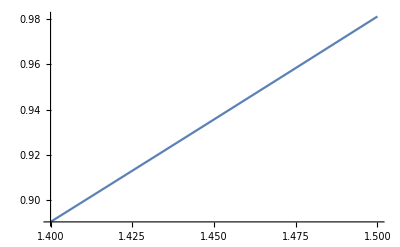

```mathematica
Plot[mwu[x],{x,1.4,1.5}]
```

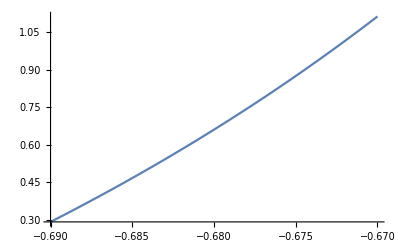

```mathematica
Plot[mwu[x],{x,-0.69,-0.67}]
```

```mathematica
0.939
```

```mathematica
mwu[-0.67358]
```

0.938979-4.83407×10^-18 ⅈ

```mathematica
mwu[1.454]
```

0.939244+0. ⅈ

```mathematica
mwu[1.58]
```

1.05451+0. ⅈ

```mathematica
mwu2[MM_]=Simplify[Expand[mre+MM^2]];
```

```mathematica
0.939*0.939
```

0.881721

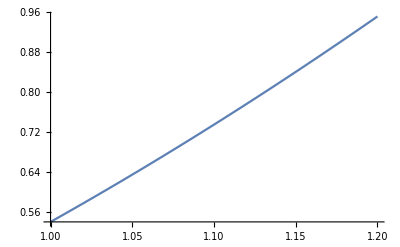

```mathematica
Plot[mwu2[x],{x,1,1.2}]
```

```mathematica
mwu2[1.1687]
```

0.88176+0. ⅈ

```mathematica
Sqrt[1.168]
```

1.08074